# Twitter Graph Models

Daniel Gladstone

University of Rhode Island

Abstract

Twitter users are inadvertent cohorts in the perpetual construction of an global dataset. This paper demonstrates that the structure of this living laboratory can be examined with computer generated graph models. The collecting algorithms developed for this purpose have access to public archives which contain all of the nearly 58 million Tweets generated each day. The principle challenge in understanding this social network has been in the development and refinement of these collecting algorithms. Graph theory theorems have been applied to graphs that were generated from which rudimentary conclusions can be drawn. This project should serve as a building block for future analysis of the graph structures contained in the Twitter social network.

4/3/13

### 1. Introduction

Social networks have existed for as long as information has been exchanged between individuals. Geographically, large networks have been growing increasingly faster since the messenger services of ancient times. Analysis of social networks by means of interdisciplinary study has a long history in applied and theoretical settings[2]. During the past century, the rapid development of communication technically has created new and massive networks. Much of the worlds population has been involved by indirectly creating the billions of vertices that constitute these networks. Such global networks remained intangible when instant communication was mostly relayed by media outlets and phone conversations. The very recent advent of internet based communication has generated a new virtual and mostly uncharted global social network. 
	Any such network can be modeled by a graph G=(V,E) wherein individuals are represented by the set of vertices V and there acquaintanceships by the set of edges E. This simple property has enormous implications, because it quantifies human behavior so that it can be studied with the tools of mathematics. The research conducted in this paper has utilized that property in combination with computer automation to generate graphs. These graphs represent social networks containing upwards of ten-thousand distinct participates. 
	Though there are numerously many ways in which internet communication can be quantified and studied this paper will examine only those that have occurred on the Twitter website. Specifically this will be in form of graphs and any pertinent graph theory applications. This research establishes methods that are used to examine a small number of selected sub-graphs generated from less the a million Twitter messages. These are relatively minuscule given the tremendous number of world wide Twitter users. Parts of methods henceforth presented could be used to examine any or all of the Twitter network. Navigating and deriving meaningful observations from Twitter’s uncharted virtual landscape remains an open challenge.

### 2. Methods

#### 2.1 Terminology

##### 2.1.1 Twitter Related Definition

Twitter is a world wide company,website, and service in which users post messages that are publicly viewable. These messages are referred to as Tweets and the acting of posting such Tweet is referred as Tweeting. The term has many arbitrary subjections which make it both a noun and a verb. A principal feature of a Tweet is that it’s author will often designate one or more keyword Hashtags with a hash tag prefix (i.e. #example). Many Tweets will contain multiple Hashtags and thus serving to establish a relationship between those Hashtags. Similarly a user can Tweet at another user by adding the at symbol prefix to the users name (@username). To keep Tweets under the 150 character restriction any link posted in a Tweet is abbreviated with shorthand URL. All these features are represented in the Fig. 1.

-Graphics-

Figure 1: Anatomy of a Tweet including Hashtags, #URI, #GWS, #Latina, and #Feminist.

##### 2.1.2 Graph Theory Terms

A graph G = (V,E) models a given social network. In this paper, G is constructed from a set vertices with each vertex V representing a Hashtag. A edge E between two vertices represents the connection made between two Hashtags contained in a single Tweet or Tweets. These edges form directed graphs(more on this in 2.2.3). This generates significant social networking implications because these graphs demonstrate how ideas/emotions/expressions(in the form of Hashtags) are connected.

##### 2.1.3 General Terminology

A bot is a computer automated program that navigates and collects internet content. The instruction it follows come in the form of an algorithm. The path the algorithm directs is made using the search query in discrete steps.  The specification of each query can be adjust to yield Tweets made at specified location and time periods with a limit of 5,000 per query. The search Hashtag that yields those results will be referred to as the seed. Many of the algorithms presented are in the Wolfram Language form and include explanations.

#### 2.2 Collection Methods

##### 2.2.1 Graph Structure and Bot Navigation

The nontrivial relationship between Hashtags can be understood in Fig. 1. There are four Hashtags that have been effectively connected; #URI, #GWS, #Latina, and #Feminist. Say this is the only Tweet in existence. The bot would generate the graph in Fig. 2 a  when given the following parameters; Query{#Latina}, VertexDegrees[3], Level[1]. If these parameters were adjusted to leval[2] the bot would then query #URI, #GWS, and #Feminist. Each respective vertex would add four edges as in Fig. 2 b. In application, each query often yields a plethora of Tweets from which the bot would pick three most frequently occurring Hashtags. 
	Given these options (vertex degrees and levels) the first operational consideration is determining how many queries need to be made. This is a counting problem that can be solved by a algorithm. Clearly, Fig. 2 a requires one query, Fig.2b requires four queries, and adding an additional level would require 13 queries. After observation we can see that given a set of vertices {V_0,V_1,V_2,...,V_n}, the number of queries Q required by each vertex is . Given D=(Degrees per Vertex) then Q=(D n +1). The more complicated dilemma arises when determining how many n are needed such that every Hashtag is queried. In the case of Fig 2.1a, how can we systemically determine that 13 queries are needed to generate Fig. 2 b. The algorithm that solves this problem and it’s explanation are in Appendix Section I.

-Graphics--Graphics-

-Graphics-

Figure 2: Network Growth in (a) is level[2] and in (b) is level[3].

##### 2.2.1 Graph Assortativity Coefficient

The graph assortativity coefficient represents the preference of a graphs vertices to have a similar degree. In Fig 2. a and Fig 2. b the assortativity coefficients are zero. In Fig 2. c the coefficient would is 1/3. n mathematica a graph with  edges and adjacency matrix entries . In Mathematica the assortativity coefficient is given by

∑_(_(i j)) (a_(i,j-)(d_i d_j)/(2m)) f_(i,j))/(∑_(_(i j)) (d_i δ_(i,j)-(d_i d_j)/(2m)) f_(i,j))

where d_i is the out-degree for the vertex v_i and δ_(i,j) is 1 if there is an edge from v_i to v_j and 0 otherwise.

##### 2.2.2 Collection and Filtering

Mathematics provides a variety of build operations to import data from the web and there are many ways in which Twitter data can be received. Many websites offer an Application Program Interface which entails server access for programs with special permission. Third party developers must establish a developer account in order to use an API’s service and the special API designated URLs are not accessible via a web browser. During the course of this project it was discovered that the Twitter API generates inconsistent data with regards to designating query time periods. As such Twitter’s official indexing partner, TOPSY.com, was used for this research.
	Upon achieving a collection method the data must be filtered and pertinent information retrieved. The # symbol provided relatively easy to use indicator extraction. Though the # symbol was easy to identify many other identifiers could be substituted. There is a large library of word analysis code for Mathemetica which could for the same purpose.

##### 2.2.4 Time

It was only very recently that I began effectively manipulating the time restrictions in the search query. These algorithms have successfully been able to query along a set timeline. That is the ability to examine what the Twitter network was doing throughout the course of an event. This has opened the door to studying past events. In addition this gives us a control data set to query from which better algorithms can be developed.

##### 2.2.3 Managing Data

Once there is a list of Hashtags, the most pertinent ones will be identified. Frequency was method chosen here though other characteristics could be substituted. The number of Hashtags chosen from the query is equal to the number of degrees in each vertex. The syntax for which these results are organized in of interest. For the Case of Fig2.1 the syntax would be #Latina→#Uri, #Latina→#Feminist, and #Latina→#GWS. This generates a graph with directed vertices. In the application of the bot only the most common Hashtags are extracted to become vertices.

#### 2.3 Regarding Data

##### 2.3.1 Development

During the course of this research there was a constant balancing act between run time and programming time. Many of the data sets that were collected required multiple day periods to be executed. Often times these programs would yield results that were unusable or un-interesting. Rarely did I bother to tune an algorithm. Instead I often pointed towards a new area of the network or used a new method collection. 
	Such a sporadic approach was necessary for the development of my own programming knowledge. However it did make finding interesting data a game of chance. In future studies a more systematic methodology should be set forth and record of results should be kept. I began this study under the assumption that an efficient bot would simply collect a massive amount of data that would inevitably contain interesting information. My thinking was flawed in to distinct ways; I did not have the computing power to look at a significantly large portion of the Twitter network and I did not have enough time to tune my algorithms to better examine the small sections of the network. 
	Studies such as Happiness and the Pattern of Life have examined relatively small regions of Twitter while looking for specific patterns. This requires a great deal of programming. Other studies such as Twitter reciprocal reply networks collect large amounts of Tweets to find meaningful results. In that particular study over 100 million Tweets were collected.

##### 2.3.2 Runtime and Development Abilities

A black box is system for which the inputs and outputs are known without knowledge of it’s internal workings. Many of the early algorithms constructed for this study where oversized black boxes; running for days with know incremental reporting until yielding a final product containing thousands of Tweets. It was only very recently that I began incorporating export features into the loops so that I could monitor the results as they were generated. This advent in combination with incrementally changing time restrictions will likely yield more substantial results.

### 4. Results

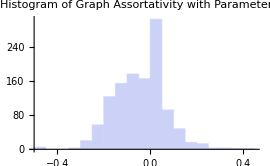
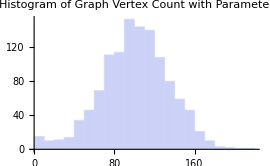
{{0.094657,159},{0.,134},{0.,50},{-0.0156564,164},{0.,151}}"Sample of Graphs Generated from Parameters α with labels {Assortativity, VertexCount}"
-Graphics--Graphics-

Figure 3: α = { VertexDegree[3],  Level[7] }

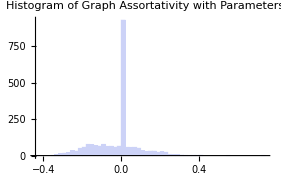
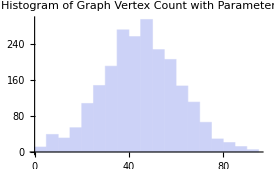
{{-0.0382532,67},{0.,70},{0.,35},{0.0515509,64},{0.,54}}"Sample of Graphs Generated from Parameters β with labels {Assortativity, VertexCount}"

-Graphics--Graphics-

Figure 4: β =  { VertexDegree[3],  Level[5] }

### 5. Discussion

Fig. 3 and Fig. 4 show Tweets collected under identical restrictions using a slightly varied algorithm. Both algorithms looked at behavior of the Hashtag #boston during ten minute windows starting on April 14, 2013 and ending on April 16, 2013. The histograms represent data from 432 graphs and the first five graphs from that sample are displayed. 
	The difference between the results comes from an adjustment in the number of levels the bot was instructed to query. In α the degree was seven which requires 1093 queries per graph (using the algorithm from Appendix 1.1). In β the level was set five thereby each required only 121 queries. Thus it would be reasonable to hypothesis a graph from the bot operating under the α conditions would contain roughly 9 times more vertices. 
	However the histograms of vertex count demonstrate that average vertex count differs only by a factor of about two. This indicates that when the α bot had mapped the entire network as it existed during the set time period. Here we have observed that a Twitter network has a finite size in a given time period. The abstract implication is that there exists a time period in where there were isolated graphs and not sub-graphs. 
	The logical question that arises from this observation is how to optimize the number of queries the algorithm makes. The assortativity histograms shows a higher a more rounded distribution which would indicate a more interactive network. Further controlled studied need to run in order to better quantify this relationship.

#### 6. Conclusion

The amorphous and mostly unknown structure of the Twitter network makes it prime for new discoveries.  The methods and results discussed here should be a building block for future studies and applications of graph theory. The project has been a tremendous learning process where my own notions  regarding graph structures, sociology, discrete math, and computer science were developed. Future studies in this area should be a collaborative effort that can build upon this information.

Appendix

### 1. Counting Problem

```mathematica
depth=3;(*How many levels of vertice*)
dd=3;(*Number of degrees per vertices*)

x[1]=1;

Do[
x[n+1]=dd*x[n]+1;
,{n,depth}];

nn=x[depth] (*Requeied queries*)
```

13

#### 2. Community Graphs

##### 2.2 Generated from #USA

VertexDegree[3], Leval [9], Queries[9841].

##### 2.3 Generated from #oboma

VertexDegree[4], Leval [5], Queries[156].

References

[1] Bagrow, J. P., Desu, S., Frank, M. R., Manukyan, N., Mitchell, L., Reagan, A., ... & Bongard, J. C. (2013). Shadow networks: Discovering hidden nodes with models of information flow. arXiv preprint arXiv:1312.6122.

[2] Mitchell, L., Frank, M. R., Harris, K. D., Dodds, P. S., & Danforth, C. M. (2013). The geography of happiness: Connecting Twitter sentiment and expression, demographics, and objective characteristics of place. PloS one, 8(5), e64417.

[3] Frank, M. R., Mitchell, L., Dodds, P. S., & Danforth, C. M. (2013). Happiness and the patterns of life: a study of geolocated tweets. Scientific reports, 3.

[4] Bliss, C. A., Kloumann, I. M., Harris, K. D., Danforth, C. M., & Dodds, P. S. (2012). Twitter reciprocal reply networks exhibit assortativity with respect to happiness. Journal of Computational Science, 3(5), 388-397.

[5] Rosen, K. (2007). Discrete Mathematics and Its Applications. New York, NY: McGrawHill.